# Scattering Kernels in 3D

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Lambertian Sphere

geometrical optics far-field phase function of a white Lambertian sphere in 3D:
[Lambert 1760] - Photometria - Part VI - p470 - §1059
[Schoenberg 1929] - doi: 10.1007/978-3-642-90703-6_1
[Esposito and Lumme 1977, Blinn 1982, Porco et al. 2008]

```mathematica
pLambertSphere[u_]:=(2 (√(1-u^2)-u ArcCos[u]))/(3 π^2)
```

From Lambert’s work in latin:

Lambert’s table:

```mathematica
Table[{t,Pi pLambertSphere[Cos[t/180 Pi]]},{t,0,180,10}]//N//TableForm
```

```mathematica
{{0., 0.}, {10., 0.0003749265567811918}, {20., 0.002972067797415395}, {30., 0.009878250529659252}, {40., 0.022915701605859425}, {50., 0.04352493713274053}, {60., 0.07266518736281957}, {70., 0.11073707843638177}, {80., 0.15753138394817434}, {90., 0.2122065907891938}, {100., 0.2732968357261279}, {110., 0.33875050732016093}, {120., 0.4059985206961529}, {130., 0.47205001025710003}, {140., 0.5336119970185115}, {150., 0.5872285197192851}, {160., 0.629433814988021}, {170., 0.6569134285649197}, {180., 0.6666666666666666}}-Graphics-
```

Thanks for Lionel Simonot for pointing me to Lambert’s work for this phase function.

### MC testing

sample uniformly from a Disk in the [x,y] plane in 3D (z = 0)

```mathematica
DiskSample3D[]:=√RandomReal[]{Cos[#],Sin[#],0}&[RandomReal[] 2 Pi]
```

project down onto a 3D sphere, build a coordinate frame, and sample a white Lambertian BRDF

```mathematica
lambertspheresample[]:=Module[{p,Z,X,Y,w,s},
p=DiskSample3D[];
p[[3]]=√(1-p[[1]]^2-p[[2]]^2);
(* building basis, X,Y,Z *)
Z=p;
X=Normalize[Cross[Z,{1,0,0}]];
Y=Cross[X,Z];
(* sample Lambertian reflectance *)
w=√RandomReal[];
p=RandomReal[{0,2Pi}];
s=√(1-w^2);
(* rotate into space of selected sphere normal p *)
-(s Cos[p] X + s Sin[p] Y + w Z)
]
```

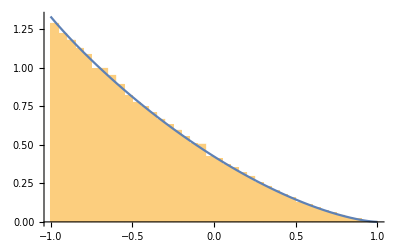

```mathematica
Show[
Histogram[Table[lambertspheresample[][[3]],{i,Range[100000]}],50,"PDF"],
Plot[2 Pi pLambertSphere[u],{u,-1,1}]
]
```

### Normalization condition

```mathematica
Integrate[2 Pi pLambertSphere[u],{u,-1,1}]
```

1

### forward scattering probability

```mathematica
Clear[u];Integrate[2 Pi pLambertSphere[u],{u,0,1}]
```

1/6

### Mean cosine (g)

```mathematica
Integrate[2 Pi pLambertSphere[u]u,{u,-1,1}]
```

-4/9

### Mean square cosine

```mathematica
Integrate[2 Pi pLambertSphere[u] u^2,{u,-1,1}]
```

3/8

This phase function is not particularly well approximated by Henyey Greenstein:

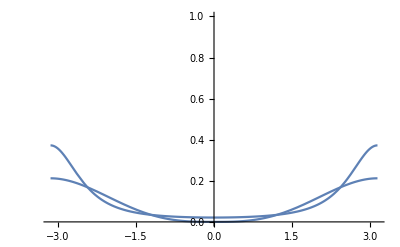

```mathematica
Show[
Plot[pHG[Cos[t],-4/9],{t,-Pi,Pi},PlotRange->{0,1}],
Plot[pLambertSphere[Cos[t]],{t,-Pi,Pi},PlotRange->All]
]
```

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2k+1)pLambertSphere[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi}]
```

1

```mathematica
Integrate[2Pi(2k+1)pLambertSphere[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi}]
```

-4/3

```mathematica
Integrate[2Pi(2k+1)pLambertSphere[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->2,{y,0,Pi}]
```

5/16

```mathematica
Integrate[2Pi(2k+1)pLambertSphere[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->3,{y,0,Pi}]
```

0

```mathematica
Integrate[2Pi(2k+1)pLambertSphere[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->4,{y,0,Pi}]
```

1/64

```mathematica
Integrate[2Pi(2k+1)pLambertSphere[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->6,{y,0,Pi}]
```

13/4096

```mathematica
Integrate[2Pi(2k+1)pLambertSphere[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->8,{y,0,Pi}]
```

17/16384

```mathematica
Integrate[2Pi(2k+1)pLambertSphere[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->10,{y,0,Pi}]
```

343/786432

### Importance sampling:

The cosine of deflection can be sampled from:

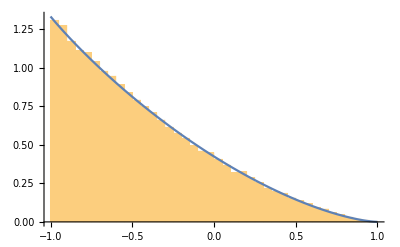

```mathematica
Show[
Histogram[Table[
Sin[2 Pi RandomReal[]] √((1-#1)(1-#2))-√(#1 #2)&[RandomReal[],RandomReal[]]
,{i,Range[100000]}],50,"PDF"],
Plot[2 Pi pLambertSphere[u],{u,-1,1}]
]
```

Approximate CDF inverse:

```mathematica
lambertSphereApproxCDFi[x_]:=1-2 (1-x^(1.01938+0.0401885 x))^0.397225
```

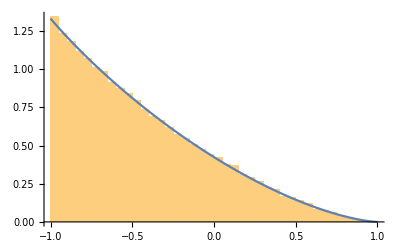

```mathematica
Show[
Histogram[Table[
lambertSphereApproxCDFi[RandomReal[]]
,{i,Range[100000]}],50,"PDF"],
Plot[2 Pi pLambertSphere[u],{u,-1,1}]
]
```